```mathematica
s1=NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2}]
```

{{y→InterpolatingFunction[{{0.,2.}},<>]}}

```mathematica
Table[y[x]/.%,{x,0,2}]
```

{{1.},{2.71828},{7.38906}}

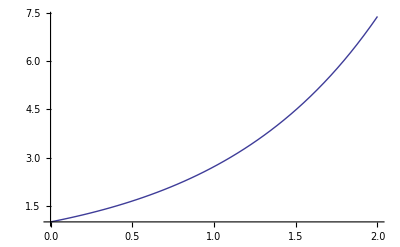

```mathematica
Plot[Evaluate[y[x]/.s1],{x,0,2},PlotRange->All]
```

```mathematica
s2=NDSolve[{y'[x]==z[x],z'[x]==-y[x],y[0]==0,z[0]==1},{y,z},{x,0,Pi}]
```

{{y→InterpolatingFunction[{{0.,3.14159}},<>],z→InterpolatingFunction[{{0.,3.14159}},<>]}}

```mathematica
z[2]/.s2
```

{-0.416147}

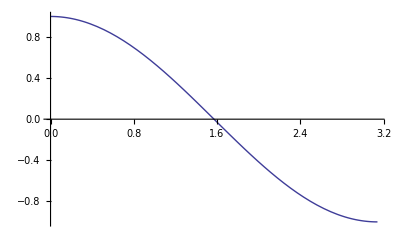

```mathematica
Plot[Evaluate[z[x]/.s2],{x,0,Pi}]
```

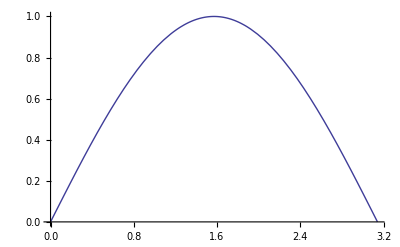

```mathematica
Plot[Evaluate[y[x]/.s2],{x,0,Pi}]
```

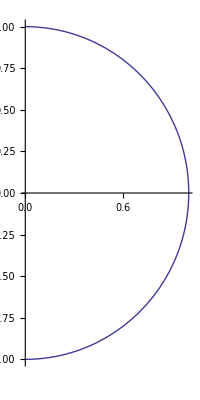

```mathematica
ParametricPlot[Evaluate[{y[x],z[x]}/.s2],{x,0,Pi},PlotRange->All]
```

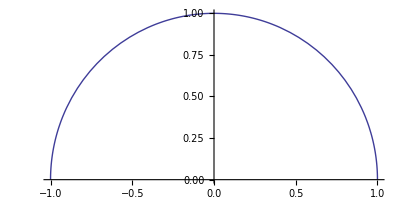

```mathematica
ParametricPlot[Evaluate[{z[x],y[x]}/.s2],{x,0,Pi},PlotRange->All]
```

```mathematica
gamma=(1/10)
```

1/10

```mathematica
eta=1
```

1

```mathematica
delta=(1/4)
```

1/4

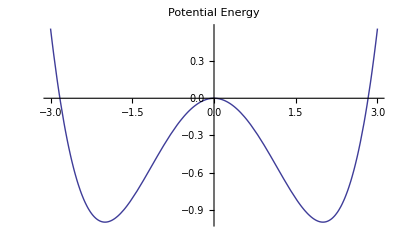

```mathematica
Plot[-(1/2)eta x^2+(1/4) delta x^4,{x,-3,3},PlotRange->All,PlotLabel->"Potential Energy"]
```

```mathematica
s3=NDSolve[{x'[t]==y[t],y'[t]==- gamma y[t]+ eta x[t]- delta x[t]^3,x[0]==3,y[0]==10},{x,y},{t,0,100}]
```

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>]}}

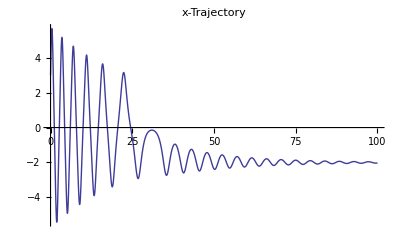

```mathematica
Plot[Evaluate[x[t]/.s3],{t,0,100},PlotRange->All,PlotPoints->500,PlotLabel->"x-Trajectory"]
```

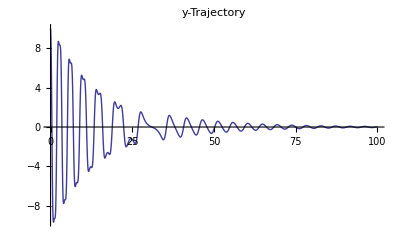

```mathematica
Plot[Evaluate[y[t]/.s3],{t,0,100},PlotRange->All,PlotPoints->500,PlotLabel->"y-Trajectory"]
```

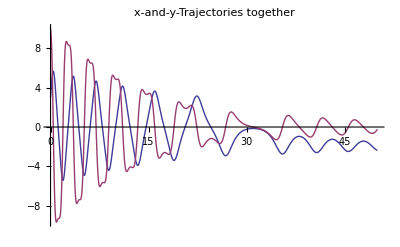

```mathematica
Plot[Evaluate[{x[t],y[t]}/.s3],{t,0,50},PlotRange->All,PlotPoints->500,PlotLabel->"x-and-y-Trajectories together"]
```

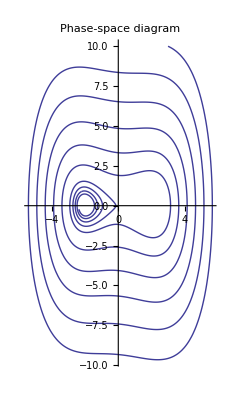

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s3],{t,0,50},PlotRange->All,PlotPoints->500,PlotLabel->"Phase-space diagram"]
```

```mathematica
nu=1
```

1

```mathematica
DF=Sin[nu t]
```

Sin[t]

```mathematica
s4=NDSolve[{x'[t]==y[t],y'[t]==- gamma y[t]+ eta x[t]- delta x[t]^3+DF,x[0]==0,y[0]==0},{x,y},{t,0,100}]
```

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>]}}

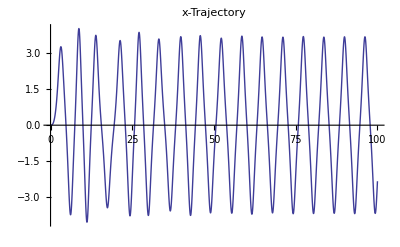

```mathematica
Plot[Evaluate[x[t]/.s4],{t,0,100},PlotRange->All,PlotPoints->500,PlotLabel->"x-Trajectory"]
```

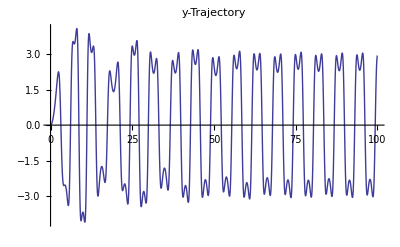

```mathematica
Plot[Evaluate[y[t]/.s4],{t,0,100},PlotRange->All,PlotPoints->500,PlotLabel->"y-Trajectory"]
```

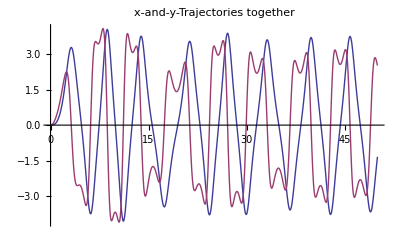

```mathematica
Plot[Evaluate[{x[t],y[t]}/.s4],{t,0,50},PlotRange->All,PlotPoints->500,PlotLabel->"x-and-y-Trajectories together"]
```

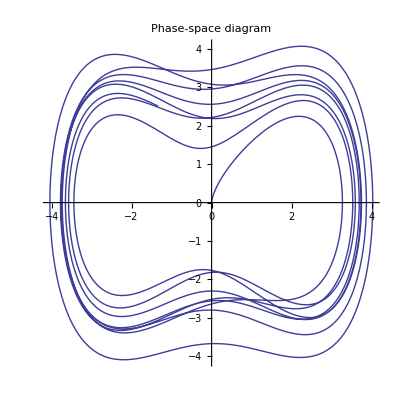

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s4],{t,0,50},PlotRange->All,PlotPoints->500,PlotLabel->"Phase-space diagram"]
```

```mathematica
nu=2
```

2

```mathematica
F0=2.5
```

2.5

```mathematica
DF=F0 Sin[nu t]
```

2.5 Sin[2 t]

```mathematica
s5=NDSolve[{x'[t]==y[t],y'[t]==- gamma y[t]+ eta x[t]- delta x[t]^3+DF,x[0]==0,y[0]==0},{x,y},{t,0,100}]
```

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>]}}

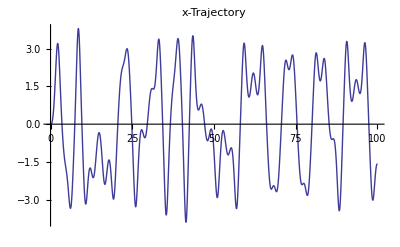

```mathematica
Plot[Evaluate[x[t]/.s5],{t,0,100},PlotRange->All,PlotPoints->500,PlotLabel->"x-Trajectory"]
```

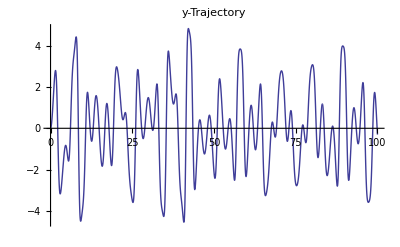

```mathematica
Plot[Evaluate[y[t]/.s5],{t,0,100},PlotRange->All,PlotPoints->500,PlotLabel->"y-Trajectory"]
```

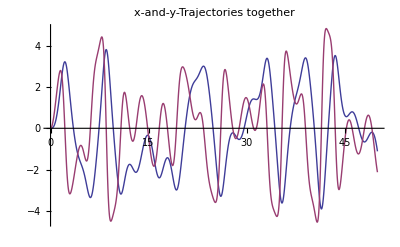

```mathematica
Plot[Evaluate[{x[t],y[t]}/.s5],{t,0,50},PlotRange->All,PlotPoints->500,PlotLabel->"x-and-y-Trajectories together"]
```

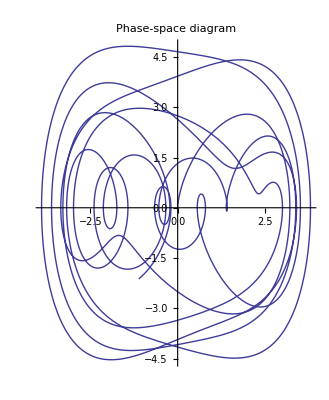

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s5],{t,0,50},PlotRange->All,PlotPoints->500,PlotLabel->"Phase-space diagram"]
```

```mathematica
p=-b/(2m);
```

```mathematica
DHM[m_,k_,b_]=NDSolve[{x'[t]==v[t],m v'[t]+b v[t]==-k x[t],x[0]==1,v[0]==p},{x,v},{t,0,20}];
```

NDSolve::ndinnt: Initial condition -0.5` b/m is not a number or a rectangular array of numbers.

```mathematica
s6=DHM[10,2,11]
```

{{x→InterpolatingFunction[{{0.,20.}},<>],v→InterpolatingFunction[{{0.,20.}},<>]}}

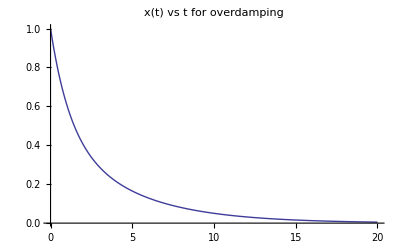

```mathematica
Plot[Evaluate[x[t]/.s6],{t,0,20},PlotRange->All,PlotPoints->500,PlotLabel->"x(t) vs t for overdamping"]
```

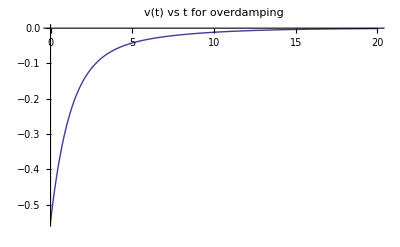

```mathematica
Plot[Evaluate[v[t]/.s6],{t,0,20},PlotRange->All,PlotPoints->500,PlotLabel->"v(t) vs t for overdamping"]
```

```mathematica
s7=DHM[10,2,3]
```

{{x→InterpolatingFunction[{{0.,20.}},<>],v→InterpolatingFunction[{{0.,20.}},<>]}}

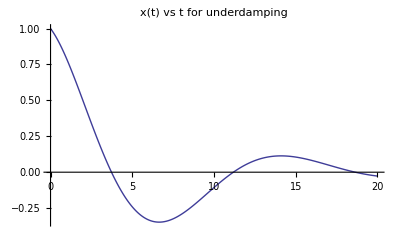

```mathematica
Plot[Evaluate[x[t]/.s7],{t,0,20},PlotRange->All,PlotPoints->500,PlotLabel->"x(t) vs t for underdamping"]
```

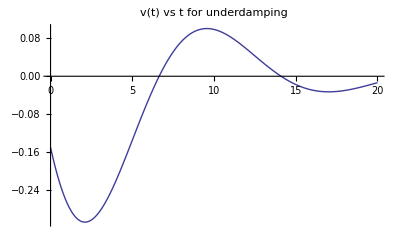

```mathematica
Plot[Evaluate[v[t]/.s7],{t,0,20},PlotRange->All,PlotPoints->500,PlotLabel->"v(t) vs t for underdamping"]
```

```mathematica
A=0.9;
```

```mathematica
B=0.65;
```

```mathematica
s8=NDSolve[{x'[t]==A+x[t]^2y[t]-(B+1)x[t],y'[t]==B x[t]-x[t]^2y[t],x[0]==0.5,y[0]==0.8},{x,y},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],y→InterpolatingFunction[{{0.,10.}},<>]}}

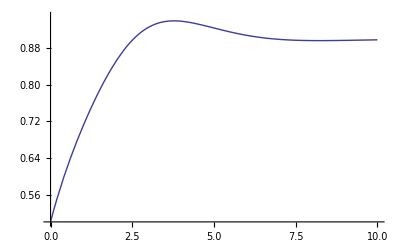

```mathematica
Plot[Evaluate[x[t]/.s8],{t,0,10},PlotRange->{0.5,0.95}]
```

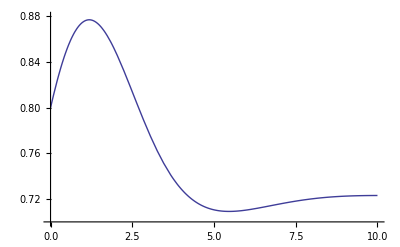

```mathematica
Plot[Evaluate[y[t]/.s8],{t,0,10},PlotRange->{0.7,0.88}]
```

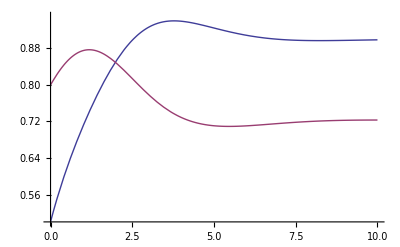

```mathematica
Plot[Evaluate[{x[t],y[t]}/.s8],{t,0,10},PlotRange->{0.5,0.95}]
```

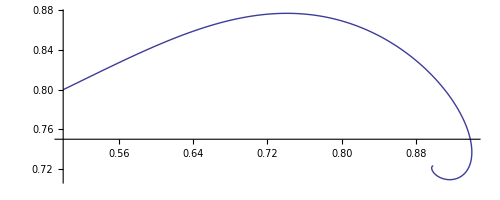

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s8],{t,0,10},PlotRange->All,PlotPoints->500]
```